```mathematica
Inclusion of drive frequency in steady state
```

drive frequency in Inclusion of state steady

```mathematica
ResourceFunction["MaTeXInstall"][]
<<MaTeX`
```

Paclet[MaTeX,1.7.9,<>]

```mathematica
(** cgs units **) 
(** constants **)
c=29979245800;
(*ℏ=1.0546*10^-27;*)
ℏ=6.582119569*10^-16; (* [eV*s] *)
e=4.8032*10^-10;
```

```mathematica
(** Parameters [rad/s] **)
wp=1.4321*10^15;
γp=0.0412*10^13+9.4498*10^13;
wc[U_,Nc_]:=(wp-3.0385*10^13)+U*Nc
γc=0+2.6435*10^9;
g=5.0440*10^11;
wc[U,1]
Δc[ω_,U_,Nc_]:= ω-(wc[U,Nc]-ⅈ*γc/2)
Δp[ω_]:= ω-(wp-ⅈ*γp/2)
Edrive[na_]:=Sqrt[na] * Abs[(ⅈ*γc/2*Δp[wc[U,0]] - g^2)]/g
```

1.40172×10^15+U

```mathematica
(**Fano Param**)
ζp[ω_]:=g^2/((ω-wp)^2+(γp/2)^2)
ζc[ω_,U_,Nc_]:=g^2/((ω-wc[U,Nc])^2+(γc/2)^2)
Ω[ω_,U_,Nc_]:= wc[U,Nc] + ζp[ω](ω-wp)
Γc[ω_]:=γc+(ζp[ω]*γp)
Γp[ω_,U_,Nc_]:=γp+(ζc[ω,U,Nc]*γc)
ϵ[ω_,U_,Nc_]:=(ω-Ω[ω,U,Nc])/(Γc[ω]/2)
q[ω_,U_,Nc_]:=-(wc[U,Nc]-ⅈ*γc/2-Ω[ω,U,Nc])/(Γc[ω]/2)
```

## Spectrum

```mathematica
βss[ω_,U_,Nc_]:=Γp[ω,U,Nc]/γp*Abs[(q[ω,U,Nc]+ϵ[ω,U,Nc])/(ϵ[ω,U,Nc]+ⅈ)]^2
αss[ω_,U_,Nc_,na_]:=g^2(Edrive[na])^2/Abs[(Δc[ω,U,Nc]*Δp[ω]-g^2)]^2
```

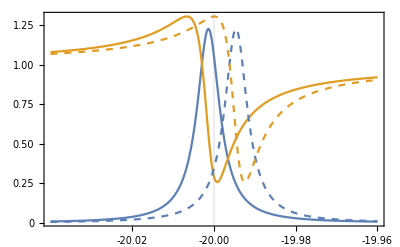

```mathematica
Plot[{αss[(det*10^-3/ℏ+wp),U,0,1],βss[(det*10^-3/ℏ+wp),U,0],
αss[(det*10^-3/ℏ+wp),Γc[wc[U,0]],1,1],βss[(det*10^-3/ℏ+wp),Γc[wc[U,0]],1]},{det,-20.04,-19.96},
GridLines->{{{-20,Thick}}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"S(\\omega_L)",None},
{"\\hbar(\\omega_L - \\omega_p) \\:\\mathrm{meV}",None}},
PlotLegends->MaTeX@
{"<a^{\\dagger}a>","\\frac{<b^{\\dagger}b>_g}{<b^{\\dagger}b>_{g=0}}"},
PlotLabel->MaTeX@
"\\omega_{L}=\\omega_c",
FrameTicks->All,
FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
PlotRange->All,
PlotStyle->{{ColorData[97,1]},{ColorData[97,2]},
{Dashed,ColorData[97,1]},{Dashed,ColorData[97,2]}},
 Exclusions->None]
```

### Relation between Fano resonance shift and chi3 (n2), with regards to the local intensity (I)

```mathematica
λ=1566*10^-7; (* [cm] *)
k=2*π/λ;
n0=1.444; (* [1] *)
n2=1.15*10^-12;(* [cm^2/W] *)
Γ=6.25*10^-6/ℏ ;(* [rad/s] *)
Intensity=Γ/(c*k*n2);
```

Null^2

Null^4

```mathematica
√16
```

4

```mathematica
(wp-20*10^-3/ℏ)
```

1.40171×10^15

```mathematica
20*10^-3/ℏ
```

3.03853×10^13

```mathematica
αss[,U,0,1]
```

1.02193×10^47/Abs[-2.54419×10^23+((-1.4321×10^15+4.7455×10^13 ⅈ)+Null) ((-1.40172×10^15+1.32175×10^9 ⅈ)+Null)]^2

```mathematica
Edrive[na]^2
```

```mathematica
g^2*4.01669992231624*^23 na^2
```

1.02193×10^47 na^2

```mathematica
Plot[Abs[(Δc[(Δp*10^-3/ℏ+wp),U,0]*Δp[(Δp*10^-3/ℏ+wp)]-g^2)]^2,{Δp,-20.04,-19.96}]
```

-Graphics-